## Prolog

I use the displayed values in your original notebook to estimate the distribution characteristics of your variables in order to simulate similar sized datasets.  There are only 6 values each for the coordinate and velocity sample distributions and 76 values for the LMC tag data.  I use Mathematica’s “EstimatedDistribution” function and assume that the generating processes for both the coordinates and the velocities are approximated by a Multivariate Normal Distribution.  Then I use the estimated mean vectors and covariance matrices to simulate 168,357 data points.  I then  use “FindDistributionParameters to see determine the mean vectors and covariance matrices of the simulated data.  Of course this is crude.  But it allows me to test my code suggestions against datasets of the same size.

For the LMC tag data, I used your analysis to generate a vector of {-1 and 1} to weighted to produce the same percentage of LMC particles in the same sized vector.

This code and the generated data are at the bottom of the file and are initialized automatically.

```mathematica
generatedData={dmCords00RV,dmVels00RV,dmTag00RV};
```

## Notes on alternate code formulations

### CHECKING NUMBER OF LMC PARTICLES

Use Count in place of your For loop.  Count counts the elements of a list by pattern matching.  It counts any value, symbolized by the  pattern “x_ “ that meets the Condition (“/;” ) of x == - 1.  You can use the operator form if it makes more sense to you, i.e., “Count x’s, where x ≤ 1 in the ‘dmTag00’ list (or array or association, etc.)”.  First, I create a random sample of tags (either -1 or 1) weighted by the percentage in your work.

```mathematica
nLMC=Count[dmTag00RV,x_/;x<=-1]
Count[x_/;x==-1][dmTag00RV]   (* Operator form *)
N[nLMC/simuationSize,2]
```

28664

28664

0.17

### SELECTING THE X-Y COORDINATES FOR DATA DISPLAY

```mathematica
dmCords00xy=dmCords00RV⟦All,1;;2⟧;
```

Use the Part command with ALL instead of the Table command (which is a Do loop) to select the columns of your coordinates matrix.  When the columns are beside one another you can use the convenient shorthand with “;;” (e.g., x and y).  When the columns are separated by intervening columns, use a List  to indicate which columns are to be selected (eg.g, x & z).

```mathematica
Timing[dmCords00xy=Table[{dmCords00RV[[i]][[1]],dmCords00RV[[i]][[2]]}, {i,1,Length[dmCords00RV]}];]
```

{0.078125,Null}

```mathematica
Timing[dmCords00xy=dmCords00RV⟦All,;;2⟧;]   (* you do not need to specify 1, as in 1;;2 when selecting from the starting column *)
```

{0.,Null}

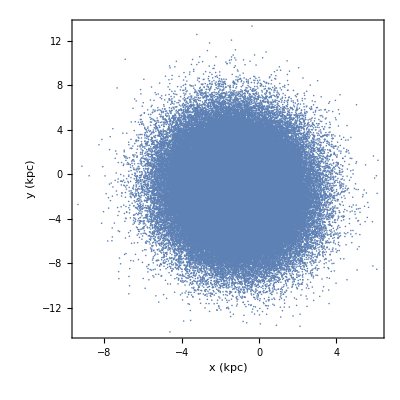

```mathematica
ListPlot[dmCords00xy, FrameLabel->{"x (kpc)","y (kpc)"}, Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1]
closeCellGroup[]
```

```mathematica
Timing[dmCords00xz=dmCords00RV⟦All,{1,3}⟧;]
```

{0.,Null}

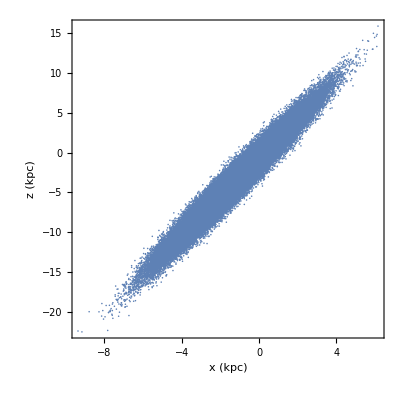

```mathematica
ListPlot[dmCords00xz, FrameLabel->{"x (kpc)","z (kpc)"}, Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1]
closeCellGroup[]
```

### MW-Only and LMC-Only Cuts

I would first use Join (or Part commands and Transform)  to combine your tags,  coordinates and velocities into one dataset (as you are assuming the sequence of data in each individual data set is rebated, i.e., tag “i” is for coordinates “i” and velocity “i”).  There are several ways to do this.  The Join command requires that the dmTag00 vector be a matrix, so I create a single column matrix with the Partition command.  Then use the Select command to select the data rows based on the tag value (which in this case is in column 7 of the data matrix)

```mathematica
dmData=Join[dmCords00RV,dmVels00RV,Partition[dmTag00RV,1],2];
Dimensions@dmData
dmData⟦;;10⟧//MatrixForm
```

{168357,7}

(-1.53806 | -2.14485 | -4.45947 | -101.784 | 116.828 | -221.124 | 1
-2.46846 | -1.09251 | -5.62312 | -1.35577 | -30.7594 | -168.838 | 1
-1.40521 | -1.16301 | -3.28018 | -97.542 | 69.2474 | -382.835 | 1
1.21043 | -4.25945 | 2.20549 | -97.1708 | 44.7864 | -240.613 | 1
-0.906018 | -2.33753 | -1.81596 | -161.339 | 120.913 | -193.856 | 1
-4.34177 | -2.63942 | -11.5797 | 4.2512 | 12.5154 | 4.43242 | 1
-0.127422 | -7.13794 | -2.86773 | -146.855 | 141.4 | -290.802 | 1
-2.96976 | -5.34786 | -8.91514 | 43.4162 | -57.5047 | 152.29 | 1
-0.398654 | -6.15518 | -2.30893 | -19.9806 | 23.1656 | 89.3665 | 1
-1.95131 | 4.04742 | -4.36451 | 35.1877 | -9.36332 | -2.34837 | -1)

```mathematica
lmcData=Select[dmData,#⟦7⟧==-1&];
Dimensions@lmcData
lmcData⟦;;10⟧//MatrixForm
```

{28627,7}

(-1.95131 | 4.04742 | -4.36451 | 35.1877 | -9.36332 | -2.34837 | -1
-0.439709 | 0.343953 | -2.26818 | -57.1784 | 7.83533 | -106.975 | -1
-1.59825 | -2.99645 | -3.71058 | -135.591 | 87.1024 | -560.432 | -1
-1.67754 | -9.18886 | -7.38104 | -10.19 | 9.01227 | -76.7917 | -1
-1.03709 | 0.962915 | -1.89803 | 141.476 | -131.773 | 256.452 | -1
-0.209767 | 2.95702 | -1.25923 | -181.741 | 139.473 | -459.976 | -1
-5.25832 | -1.20837 | -13.0838 | -108.111 | 56.368 | -333.282 | -1
-3.66173 | 3.69452 | -10.1897 | -146.524 | 192.126 | -298.787 | -1
-0.0507218 | -3.13599 | 0.76866 | -129.488 | 124.406 | -274.519 | -1
-2.83962 | -5.20892 | -8.29547 | 7.65664 | 69.9352 | 60.8018 | -1)

```mathematica
lmcCords00RV=lmcData⟦All,;;3⟧;
Dimensions@lmcCords00RV
lmcCords00RV⟦;;10⟧//MatrixForm
```

{28627,3}

(-1.95131 | 4.04742 | -4.36451
-0.439709 | 0.343953 | -2.26818
-1.59825 | -2.99645 | -3.71058
-1.67754 | -9.18886 | -7.38104
-1.03709 | 0.962915 | -1.89803
-0.209767 | 2.95702 | -1.25923
-5.25832 | -1.20837 | -13.0838
-3.66173 | 3.69452 | -10.1897
-0.0507218 | -3.13599 | 0.76866
-2.83962 | -5.20892 | -8.29547)

```mathematica
lmcVels00RV=lmcData⟦All,4;;6⟧;
Dimensions@lmcVels00RV
lmcVels00RV⟦;;10⟧//MatrixForm
```

{28627,3}

(35.1877 | -9.36332 | -2.34837
-57.1784 | 7.83533 | -106.975
-135.591 | 87.1024 | -560.432
-10.19 | 9.01227 | -76.7917
141.476 | -131.773 | 256.452
-181.741 | 139.473 | -459.976
-108.111 | 56.368 | -333.282
-146.524 | 192.126 | -298.787
-129.488 | 124.406 | -274.519
7.65664 | 69.9352 | 60.8018)

## Create example data sets

```mathematica
closeCellGroup[] := (SelectionMove[EvaluationCell[], Next,Cell]; 
FrontEndExecute[FrontEndToken["SelectionCloseUnselectedCells"]])
```

```mathematica
simuationSize=168357;
```

I use the displayed values in your original notebook to estimate the distribution characteristics of your variables in order to simulate similar sized datasets.  There are only 6 values each for the coordinate and velocity sample distributions and 76 values for the LMC tag data.  I use Mathematica’s “EstimatedDistribution” function and assume that the generating processes for both the coordinates and the velocities are approximated by a Multivariate Normal Distribution.  Then I use the estimated mean vectors and covariance matrices to simulate 168,357 data points.  I then  use “FindDistributionParameters to see determine the mean vectors and covariance matrices of the simulated data.  Of course this is crude.  But it allows me to test my code suggestions against datasets of the same size.

For the LMC tag data, I used your analysis to generate a vector of {-1 and 1} to weighted to produce the same percentage of LMC particles in the same sized vector.

I use the closeCellGroup[] function above to close the code cells that estimate the sample distribution values and generate the simulated datasets.  This allows the output to appear less cluttered and keeps the utility code out of the way.  To see the code, simply double click on the enclosing cell brackets.

### DM coordinate variables

Notebook data

```mathematica
MatrixForm[dmCords00={{0.016431426629424095,-0.1076788678765297,0.03446260467171669},{-0.08331732451915741,-0.005956035573035479,0.18741817772388458},{0.23650655150413513,0.05569346994161606,0.0347386933863163},{-4.803868293762207,0.7528245449066162,-11.71234130859375},{-1.302531123161316,-8.16396427154541,-4.614678382873535},{-1.0871785879135132,-0.7993932962417603,-4.996247291564941}}]
closeCellGroup[]
```

(0.0164314 | -0.107679 | 0.0344626
-0.0833173 | -0.00595604 | 0.187418
0.236507 | 0.0556935 | 0.0347387
-4.80387 | 0.752825 | -11.7123
-1.30253 | -8.16396 | -4.61468
-1.08718 | -0.799393 | -4.99625)

Estimated sample data distribution parameters

```mathematica
edistCoords=EstimatedDistribution[dmCords00, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

MultinormalDistribution[{-1.17066,-1.37808,-3.51111},{{2.96603,-0.296873,7.17307},{-0.296873,9.4127,0.63605},{7.17307,0.63605,18.2512}}]

Multivariate Normal mean and covariance from simulated data

```mathematica
dmCords00RV=RandomVariate[edistCoords,simuationSize];
fdistpar=FindDistributionParameters[dmCords00RV, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

{μ[1]→-1.16676,μ[2]→-1.38011,μ[3]→-3.49904,s[1,1]→2.97571,s[1,2]→-0.287957,s[1,3]→7.19528,s[2,1]→-0.287957,s[2,2]→9.37231,s[2,3]→0.643746,s[3,1]→7.19528,s[3,2]→0.643746,s[3,3]→18.2992}

### DM velocity variables

Notebook data

```mathematica
MatrixForm[dmVels00={{36.43170166015625,-9.138969421386719,-26.757831573486328},{-24.890954971313477,-21.605627059936523,-3.0834414958953857},{-9.940251350402832,-14.906100273132324,33.107540130615234},{-169.15914916992188,139.89755249023438,-290.9612121582031},{-104.96575164794922,120.04015350341797,-352.1723937988281},{-103.65585327148438,-1.9502073526382446,-415.2244873046875}}]
Dimensions@%
closeCellGroup[]
```

(36.4317 | -9.13897 | -26.7578
-24.891 | -21.6056 | -3.08344
-9.94025 | -14.9061 | 33.1075
-169.159 | 139.898 | -290.961
-104.966 | 120.04 | -352.172
-103.656 | -1.95021 | -415.224)

{6,3}

Estimated sample data distribution parameters

```mathematica
edist=EstimatedDistribution[dmVels00, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

MultinormalDistribution[{-62.6967,35.3895,-175.849},{{4806.26,-3732.85,10307.9},{-3732.85,4540.47,-7502.17},{10307.9,-7502.17,32896.7}}]

Multivariate Normal mean and covariance from simulated data

```mathematica
dmVels00RV=RandomVariate[edist,simuationSize];
fdistpar=FindDistributionParameters[dmVels00RV, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

{μ[1]→-62.9964,μ[2]→35.6099,μ[3]→-176.625,s[1,1]→4833.69,s[1,2]→-3754.79,s[1,3]→10383.2,s[2,1]→-3754.79,s[2,2]→4554.05,s[2,3]→-7570.51,s[3,1]→10383.2,s[3,2]→-7570.51,s[3,3]→33091.}

### LMC_tag for each DM particle variable

```mathematica
Notebook data
```

```mathematica
dmTag00={-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.};
Length@dmTag00
closeCellGroup[]
```

76

Simulated LMC tag data

```mathematica
dmTag00RV=RandomChoice[{.17,1-.17}->{-1,1},simuationSize];
Length@dmTag00RV
```

168357

```mathematica
generatedData={dmCords00RV,dmVels00RV,dmTag00RV};
```